```mathematica
fiveNodes=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]
```

{0,19683,26244,28431,29160,29403,29484,29511,29520,29523,29524,29521,29514,29515,29512,29493,29496,29497,29494,29487,29488,29485,29430,29439,29442,29443,29440,29433,29434,29431,29412,29415,29416,29413,29406,29407,29404,29241,29268,29277,29280,29281,29278,29271,29272,29269,29250,29253,29254,29251,29244,29245,29242,29187,29196,29199,29200,29197,29190,29191,29188,29169,29172,29173,29170,29163,29164,29161,28674,28755,28782,28791,28794,28795,28792,28785,28786,28783,28764,28767,28768,28765,28758,28759,28756,28701,28710,28713,28714,28711,28704,28705,28702,28683,28686,28687,28684,28677,28678,28675,28512,28539,28548,28551,28552,28549,28542,28543,28540,28521,28524,28525,28522,28515,28516,28513,28458,28467,28470,28471,28468,28461,28462,28459,28440,28443,28444,28441,28434,28435,28432,26973,27216,27297,27324,27333,27336,27337,27334,27327,27328,27325,27306,27309,27310,27307,27300,27301,27298,27243,27252,27255,27256,27253,27246,27247,27244,27225,27228,27229,27226,27219,27220,27217,27054,27081,27090,27093,27094,27091,27084,27085,27082,27063,27066,27067,27064,27057,27058,27055,27000,27009,27012,27013,27010,27003,27004,27001,26982,26985,26986,26983,26976,26977,26974,26487,26568,26595,26604,26607,26608,26605,26598,26599,26596,26577,26580,26581,26578,26571,26572,26569,26514,26523,26526,26527,26524,26517,26518,26515,26496,26499,26500,26497,26490,26491,26488,26325,26352,26361,26364,26365,26362,26355,26356,26353,26334,26337,26338,26335,26328,26329,26326,26271,26280,26283,26284,26281,26274,26275,26272,26253,26256,26257,26254,26247,26248,26245,21870,22599,22842,22923,22950,22959,22962,22963,22960,22953,22954,22951,22932,22935,22936,22933,22926,22927,22924,22869,22878,22881,22882,22879,22872,22873,22870,22851,22854,22855,22852,22845,22846,22843,22680,22707,22716,22719,22720,22717,22710,22711,22708,22689,22692,22693,22690,22683,22684,22681,22626,22635,22638,22639,22636,22629,22630,22627,22608,22611,22612,22609,22602,22603,22600,22113,22194,22221,22230,22233,22234,22231,22224,22225,22222,22203,22206,22207,22204,22197,22198,22195,22140,22149,22152,22153,22150,22143,22144,22141,22122,22125,22126,22123,22116,22117,22114,21951,21978,21987,21990,21991,21988,21981,21982,21979,21960,21963,21964,21961,21954,21955,21952,21897,21906,21909,21910,21907,21900,21901,21898,21879,21882,21883,21880,21873,21874,21871,20412,20655,20736,20763,20772,20775,20776,20773,20766,20767,20764,20745,20748,20749,20746,20739,20740,20737,20682,20691,20694,20695,20692,20685,20686,20683,20664,20667,20668,20665,20658,20659,20656,20493,20520,20529,20532,20533,20530,20523,20524,20521,20502,20505,20506,20503,20496,20497,20494,20439,20448,20451,20452,20449,20442,20443,20440,20421,20424,20425,20422,20415,20416,20413,19926,20007,20034,20043,20046,20047,20044,20037,20038,20035,20016,20019,20020,20017,20010,20011,20008,19953,19962,19965,19966,19963,19956,19957,19954,19935,19938,19939,19936,19929,19930,19927,19764,19791,19800,19803,19804,19801,19794,19795,19792,19773,19776,19777,19774,19767,19768,19765,19710,19719,19722,19723,19720,19713,19714,19711,19692,19695,19696,19693,19686,19687,19684,6561,8748,9477,9720,9801,9828,9837,9840,9841,9838,9831,9832,9829,9810,9813,9814,9811,9804,9805,9802,9747,9756,9759,9760,9757,9750,9751,9748,9729,9732,9733,9730,9723,9724,9721,9558,9585,9594,9597,9598,9595,9588,9589,9586,9567,9570,9571,9568,9561,9562,9559,9504,9513,9516,9517,9514,9507,9508,9505,9486,9489,9490,9487,9480,9481,9478,8991,9072,9099,9108,9111,9112,9109,9102,9103,9100,9081,9084,9085,9082,9075,9076,9073,9018,9027,9030,9031,9028,9021,9022,9019,9000,9003,9004,9001,8994,8995,8992,8829,8856,8865,8868,8869,8866,8859,8860,8857,8838,8841,8842,8839,8832,8833,8830,8775,8784,8787,8788,8785,8778,8779,8776,8757,8760,8761,8758,8751,8752,8749,7290,7533,7614,7641,7650,7653,7654,7651,7644,7645,7642,7623,7626,7627,7624,7617,7618,7615,7560,7569,7572,7573,7570,7563,7564,7561,7542,7545,7546,7543,7536,7537,7534,7371,7398,7407,7410,7411,7408,7401,7402,7399,7380,7383,7384,7381,7374,7375,7372,7317,7326,7329,7330,7327,7320,7321,7318,7299,7302,7303,7300,7293,7294,7291,6804,6885,6912,6921,6924,6925,6922,6915,6916,6913,6894,6897,6898,6895,6888,6889,6886,6831,6840,6843,6844,6841,6834,6835,6832,6813,6816,6817,6814,6807,6808,6805,6642,6669,6678,6681,6682,6679,6672,6673,6670,6651,6654,6655,6652,6645,6646,6643,6588,6597,6600,6601,6598,6591,6592,6589,6570,6573,6574,6571,6564,6565,6562,2187,2916,3159,3240,3267,3276,3279,3280,3277,3270,3271,3268,3249,3252,3253,3250,3243,3244,3241,3186,3195,3198,3199,3196,3189,3190,3187,3168,3171,3172,3169,3162,3163,3160,2997,3024,3033,3036,3037,3034,3027,3028,3025,3006,3009,3010,3007,3000,3001,2998,2943,2952,2955,2956,2953,2946,2947,2944,2925,2928,2929,2926,2919,2920,2917,2430,2511,2538,2547,2550,2551,2548,2541,2542,2539,2520,2523,2524,2521,2514,2515,2512,2457,2466,2469,2470,2467,2460,2461,2458,2439,2442,2443,2440,2433,2434,2431,2268,2295,2304,2307,2308,2305,2298,2299,2296,2277,2280,2281,2278,2271,2272,2269,2214,2223,2226,2227,2224,2217,2218,2215,2196,2199,2200,2197,2190,2191,2188,729,972,1053,1080,1089,1092,1093,1090,1083,1084,1081,1062,1065,1066,1063,1056,1057,1054,999,1008,1011,1012,1009,1002,1003,1000,981,984,985,982,975,976,973,810,837,846,849,850,847,840,841,838,819,822,823,820,813,814,811,756,765,768,769,766,759,760,757,738,741,742,739,732,733,730,243,324,351,360,363,364,361,354,355,352,333,336,337,334,327,328,325,270,279,282,283,280,273,274,271,252,255,256,253,246,247,244,81,108,117,120,121,118,111,112,109,90,93,94,91,84,85,82,27,36,39,40,37,30,31,28,9,12,13,10,3,4,1}

```mathematica
Length[fiveNodes]
```

1024

```mathematica
vars=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}

```mathematica
{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}
```

```mathematica
Total[Table[BaseCoeff[k,"C"],{k,fiveNodes}]]
```

{1024,512,512,512,512,512,512,512,512,512,512,128,128,128,256,256,256,128,128,256,256,256,128,256,256,256,256,256,256,128,128,256,128,256,256,128,16,16,64,16,64,64,64,16,64,64,64,64,64,64,16,1}

```mathematica
BaseCoeff2[key_]:=Table[Coefficient[allGraphs5[key,"colofour"],var],{var,vars}]
```

```mathematica
scores=Total[Table[BaseCoeff2[k],{k,fiveNodes}]]
```

{1024,512,512,512,512,512,512,512,512,512,512,128,128,128,256,256,256,128,128,256,256,256,128,256,256,256,256,256,256,128,128,256,128,256,256,128,16,16,64,16,64,64,64,16,64,64,64,64,64,64,16,1}

```mathematica
vars2=Map[Last,Table[{scores[[k]],vars[[k]]},{k,52}]//ReverseSort]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x25x3x4,v1x24x3x5,v1x23x4x5,v15x2x3x4,v14x2x3x5,v13x2x4x5,v12x3x4x5,v1x25x34,v1x24x35,v1x23x45,v15x2x34,v15x24x3,v15x23x4,v14x2x35,v14x25x3,v14x23x5,v13x2x45,v13x25x4,v13x24x5,v12x3x45,v12x35x4,v12x34x5,v1x2x345,v1x245x3,v1x235x4,v1x234x5,v145x2x3,v135x2x4,v134x2x5,v125x3x4,v124x3x5,v123x4x5,v15x234,v14x235,v145x23,v13x245,v135x24,v134x25,v12x345,v125x34,v124x35,v123x45,v1x2345,v1345x2,v1245x3,v1235x4,v1234x5,v12345}

```mathematica
vars2/.RepGraph["C"]
```

{-Graphics-295240,-Graphics-295250,-Graphics-295270,-Graphics-295330,-Graphics-295510,-Graphics-296050,-Graphics-297670,-Graphics-302530,-Graphics-317110,-Graphics-360850,-Graphics-492070,-Graphics-295600,-Graphics-296080,-Graphics-297681,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-317140,-Graphics-317380,-Graphics-319540,-Graphics-360860,-Graphics-361120,-Graphics-361660,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-295371,-Graphics-296330,-Graphics-297970,-Graphics-298571,-Graphics-324411,-Graphics-368170,-Graphics-382810,-Graphics-499631,-Graphics-514750,-Graphics-560111,-Graphics-305861,-Graphics-319840,-Graphics-326841,-Graphics-361940,-Graphics-368980,-Graphics-383080,-Graphics-492201,-Graphics-499721,-Graphics-514780,-Graphics-560121,-Graphics-298881,-Graphics-390141,-Graphics-522321,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
BaseCoeff3[key_]:=Table[Coefficient[allGraphs5[key,"colofour"],var],{var,vars2}]
```

```mathematica
Total[Table[BaseCoeff3[k],{k,fiveNodes}]]
```

{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,128,128,128,128,128,128,128,128,64,64,64,64,64,64,64,64,64,64,16,16,16,16,16,1}

```mathematica
Map[Labeled[#[[2]],Style[#[[1]],Red]]&,Table[{scores[[k]],vars[[k]]},{k,52}]//ReverseSort]
```

{v1x2x3x4x51024,v1x2x3x45512,v1x2x35x4512,v1x2x34x5512,v1x25x3x4512,v1x24x3x5512,v1x23x4x5512,v15x2x3x4512,v14x2x3x5512,v13x2x4x5512,v12x3x4x5512,v1x25x34256,v1x24x35256,v1x23x45256,v15x2x34256,v15x24x3256,v15x23x4256,v14x2x35256,v14x25x3256,v14x23x5256,v13x2x45256,v13x25x4256,v13x24x5256,v12x3x45256,v12x35x4256,v12x34x5256,v1x2x345128,v1x245x3128,v1x235x4128,v1x234x5128,v145x2x3128,v135x2x4128,v134x2x5128,v125x3x4128,v124x3x5128,v123x4x5128,v15x23464,v14x23564,v145x2364,v13x24564,v135x2464,v134x2564,v12x34564,v125x3464,v124x3564,v123x4564,v1x234516,v1345x216,v1245x316,v1235x416,v1234x516,v123451}

```mathematica
RepCount=Map[#[[2]]->{#[[1]],Style[#[[1]],Red],#[[2]]}&,Table[{scores[[k]],vars[[k]]},{k,52}]//ReverseSort]
```

{v1x2x3x4x5→{1024,1024,v1x2x3x4x5},v1x2x3x45→{512,512,v1x2x3x45},v1x2x35x4→{512,512,v1x2x35x4},v1x2x34x5→{512,512,v1x2x34x5},v1x25x3x4→{512,512,v1x25x3x4},v1x24x3x5→{512,512,v1x24x3x5},v1x23x4x5→{512,512,v1x23x4x5},v15x2x3x4→{512,512,v15x2x3x4},v14x2x3x5→{512,512,v14x2x3x5},v13x2x4x5→{512,512,v13x2x4x5},v12x3x4x5→{512,512,v12x3x4x5},v1x25x34→{256,256,v1x25x34},v1x24x35→{256,256,v1x24x35},v1x23x45→{256,256,v1x23x45},v15x2x34→{256,256,v15x2x34},v15x24x3→{256,256,v15x24x3},v15x23x4→{256,256,v15x23x4},v14x2x35→{256,256,v14x2x35},v14x25x3→{256,256,v14x25x3},v14x23x5→{256,256,v14x23x5},v13x2x45→{256,256,v13x2x45},v13x25x4→{256,256,v13x25x4},v13x24x5→{256,256,v13x24x5},v12x3x45→{256,256,v12x3x45},v12x35x4→{256,256,v12x35x4},v12x34x5→{256,256,v12x34x5},v1x2x345→{128,128,v1x2x345},v1x245x3→{128,128,v1x245x3},v1x235x4→{128,128,v1x235x4},v1x234x5→{128,128,v1x234x5},v145x2x3→{128,128,v145x2x3},v135x2x4→{128,128,v135x2x4},v134x2x5→{128,128,v134x2x5},v125x3x4→{128,128,v125x3x4},v124x3x5→{128,128,v124x3x5},v123x4x5→{128,128,v123x4x5},v15x234→{64,64,v15x234},v14x235→{64,64,v14x235},v145x23→{64,64,v145x23},v13x245→{64,64,v13x245},v135x24→{64,64,v135x24},v134x25→{64,64,v134x25},v12x345→{64,64,v12x345},v125x34→{64,64,v125x34},v124x35→{64,64,v124x35},v123x45→{64,64,v123x45},v1x2345→{16,16,v1x2345},v1345x2→{16,16,v1345x2},v1245x3→{16,16,v1245x3},v1235x4→{16,16,v1235x4},v1234x5→{16,16,v1234x5},v12345→{1,1,v12345}}

```mathematica
RepCount2=Map[#[[2]]->Style[#[[1]],Red]&,Table[{scores[[k]],vars[[k]]},{k,52}]//ReverseSort]
```

{v1x2x3x4x5→1024,v1x2x3x45→512,v1x2x35x4→512,v1x2x34x5→512,v1x25x3x4→512,v1x24x3x5→512,v1x23x4x5→512,v15x2x3x4→512,v14x2x3x5→512,v13x2x4x5→512,v12x3x4x5→512,v1x25x34→256,v1x24x35→256,v1x23x45→256,v15x2x34→256,v15x24x3→256,v15x23x4→256,v14x2x35→256,v14x25x3→256,v14x23x5→256,v13x2x45→256,v13x25x4→256,v13x24x5→256,v12x3x45→256,v12x35x4→256,v12x34x5→256,v1x2x345→128,v1x245x3→128,v1x235x4→128,v1x234x5→128,v145x2x3→128,v135x2x4→128,v134x2x5→128,v125x3x4→128,v124x3x5→128,v123x4x5→128,v15x234→64,v14x235→64,v145x23→64,v13x245→64,v135x24→64,v134x25→64,v12x345→64,v125x34→64,v124x35→64,v123x45→64,v1x2345→16,v1345x2→16,v1245x3→16,v1235x4→16,v1234x5→16,v12345→1}

```mathematica
Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v1235x4]&]
```

{0,2187,2268,2277,2278,2269,2196,2197,2188,81,90,91,82,9,10,1}

```mathematica
Map[ShowGraph5Least,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v1235x4]&]]
```

{-Graphics-034,-Graphics-218724,-Graphics-226818,-Graphics-227712,-Graphics-22788,-Graphics-226912,-Graphics-219615,-Graphics-219710,-Graphics-218816,-Graphics-8124,-Graphics-9016,-Graphics-9110,-Graphics-8215,-Graphics-921,-Graphics-1013,-Graphics-121}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v1235x4]&]]//Tally//Sort
```

{{15,1},{20,4},{27,6},{37,4},{52,1}}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v12x345]&]]//Tally//Sort
```

{{10,1},{12,6},{15,12},{16,3},{20,20},{27,15},{37,6},{52,1}}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v123x4x5]&]]//Tally//Sort
```

{{5,1},{7,6},{9,3},{10,13},{12,6},{13,12},{15,20},{16,3},{17,3},{20,32},{27,21},{37,7},{52,1}}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v12x34x5]&]]//Tally//Sort
```

{{4,1},{5,4},{6,4},{7,14},{8,12},{9,4},{10,34},{11,4},{12,16},{13,20},{15,45},{16,5},{17,4},{20,52},{27,28},{37,8},{52,1}}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],v12x3x4x5]&]]//Tally//Sort
```

{{2,1},{3,6},{4,9},{5,23},{6,9},{7,54},{8,24},{9,15},{10,79},{11,6},{12,30},{13,42},{15,75},{16,9},{17,7},{20,77},{27,36},{37,9},{52,1}}

```mathematica
v12x34x5
```

v12x34x5

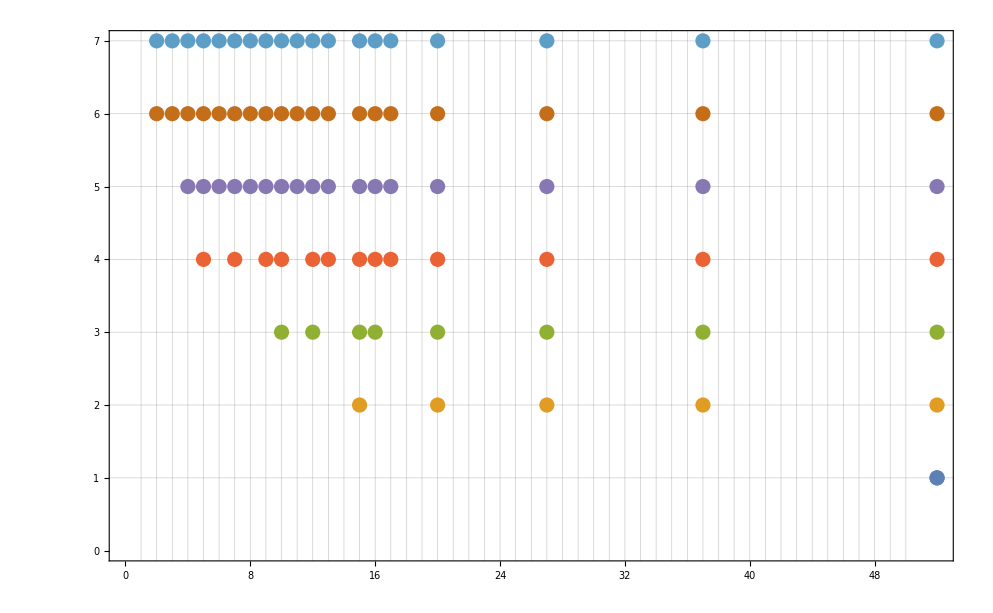

```mathematica
ListPlot[
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[Map[{#[[1]],x}&,Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]]//Tally//Sort],{x,Length[sample]}]
],GridLines->{Range[52],Range[7]},Frame->True]
```

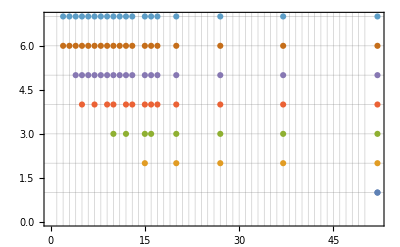

```mathematica
ListPlot[
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[Map[{#[[1]],x}&,Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,Select[fiveNodes,MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]]//Tally//Sort],{x,Length[sample]}]
],GridLines->{Range[52],Range[7]},Frame->True]
```

```mathematica
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[ShowGraph5Least[(sample[[x]]/.RepKey["C"])]->Map[ShowGraph5Least,Select[fiveNodes,Length[allGraphs5[#,"colofour"]]==27&&MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]],{x,Length[sample]}]
]//TableForm
```

-Graphics-590481→{}
-Graphics-582881→{-Graphics-75616,-Graphics-73215,-Graphics-73013,-Graphics-3018,-Graphics-2815,-Graphics-416}
-Graphics-560121→{-Graphics-291616,-Graphics-226818,-Graphics-221416,-Graphics-219615,-Graphics-219016,-Graphics-81015,-Graphics-75616,-Graphics-73813,-Graphics-73215,-Graphics-10818,-Graphics-9016,-Graphics-8416,-Graphics-3615,-Graphics-3018,-Graphics-1216}
-Graphics-560111→{-Graphics-291616,-Graphics-226818,-Graphics-221416,-Graphics-219615,-Graphics-219016,-Graphics-218816,-Graphics-81015,-Graphics-75616,-Graphics-73813,-Graphics-73215,-Graphics-73013,-Graphics-10818,-Graphics-9016,-Graphics-8416,-Graphics-8215,-Graphics-3615,-Graphics-3018,-Graphics-2815,-Graphics-1216,-Graphics-1013,-Graphics-416}
-Graphics-492161→{-Graphics-874818,-Graphics-729015,-Graphics-680416,-Graphics-664216,-Graphics-658816,-Graphics-656418,-Graphics-656215,-Graphics-291616,-Graphics-243015,-Graphics-226818,-Graphics-221416,-Graphics-219016,-Graphics-218816,-Graphics-97213,-Graphics-81015,-Graphics-75616,-Graphics-73215,-Graphics-73013,-Graphics-32416,-Graphics-27015,-Graphics-24615,-Graphics-24413,-Graphics-10818,-Graphics-8416,-Graphics-8215,-Graphics-3018,-Graphics-2815,-Graphics-416}
-Graphics-492070→{-Graphics-874818,-Graphics-729015,-Graphics-680416,-Graphics-664216,-Graphics-658816,-Graphics-657015,-Graphics-656418,-Graphics-656215,-Graphics-291616,-Graphics-243015,-Graphics-226818,-Graphics-221416,-Graphics-219615,-Graphics-219016,-Graphics-218816,-Graphics-97213,-Graphics-81015,-Graphics-75616,-Graphics-73813,-Graphics-73215,-Graphics-73013,-Graphics-32416,-Graphics-27015,-Graphics-25213,-Graphics-24615,-Graphics-24413,-Graphics-10818,-Graphics-9016,-Graphics-8416,-Graphics-8215,-Graphics-3615,-Graphics-3018,-Graphics-2815,-Graphics-1216,-Graphics-1013,-Graphics-416}
-Graphics-295240→{-Graphics-2624416,-Graphics-2187015,-Graphics-2041213,-Graphics-1992613,-Graphics-1976415,-Graphics-1971016,-Graphics-1969213,-Graphics-1968615,-Graphics-1968413,-Graphics-874818,-Graphics-729015,-Graphics-680416,-Graphics-664216,-Graphics-658816,-Graphics-657015,-Graphics-656418,-Graphics-656215,-Graphics-291616,-Graphics-243015,-Graphics-226818,-Graphics-221416,-Graphics-219615,-Graphics-219016,-Graphics-218816,-Graphics-97213,-Graphics-81015,-Graphics-75616,-Graphics-73813,-Graphics-73215,-Graphics-73013,-Graphics-32416,-Graphics-27015,-Graphics-25213,-Graphics-24615,-Graphics-24413,-Graphics-10818,-Graphics-9016,-Graphics-8416,-Graphics-8215,-Graphics-3615,-Graphics-3018,-Graphics-2815,-Graphics-1216,-Graphics-1013,-Graphics-416}

```mathematica
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[ShowGraph5Least[(sample[[x]]/.RepKey["C"])]->Map[ShowGraph5Least,Select[fiveNodes,Length[allGraphs5[#,"colofour"]]==37&&MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]],{x,Length[sample]}]
]//TableForm
```

-Graphics-590481→{}
-Graphics-582881→{-Graphics-72921,-Graphics-2724,-Graphics-324,-Graphics-121}
-Graphics-560121→{-Graphics-218724,-Graphics-72921,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324}
-Graphics-560111→{-Graphics-218724,-Graphics-72921,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121}
-Graphics-492161→{-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-324,-Graphics-121}
-Graphics-492070→{-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121}
-Graphics-295240→{-Graphics-1968321,-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121}

```mathematica
With[{sample={v12345,v1x2345,v12x345,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[ShowGraph5Least[(sample[[x]]/.RepKey["C"])]->Length[Map[ShowGraph5Least,Select[fiveNodes,Length[allGraphs5[#,"colofour"]]==37&&MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]]],{x,Length[sample]}]
]//TableForm
```

-Graphics-590481→0
-Graphics-298881→4
-Graphics-492201→6
-Graphics-560111→7
-Graphics-492161→8
-Graphics-492070→9
-Graphics-295240→10

```mathematica
allGraphs5[729,"colofour"]/.RepCount
```

{10016,2 16+6 64+7 128+12 256+9 512+1024,v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5}

```mathematica
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[ShowGraph5Least[(sample[[x]]/.RepKey["C"])]->Framed[Column[
Map[
ShowGraph5Least[#]->Part[(allGraphs5[#,"colofour"]/.RepCount),2]&
,
Select[fiveNodes,Length[allGraphs5[#,"colofour"]]==37&&MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]]]],{x,Length[sample]}]
]//TableForm
```

-Graphics-590481→
-Graphics-582881→-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-560121→-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-560111→-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-492161→-Graphics-656124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-24321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-492070→-Graphics-656124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-24321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-295240→-Graphics-1968321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-656124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-24321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024

```mathematica
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[
With[{keys=Select[fiveNodes,Length[allGraphs5[#,"colofour"]]==37&&MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]},

ShowGraph5Least[(sample[[x]]/.RepKey["C"])]->Framed[
Column[
Table[(ShowGraph5Least[current]->(allGraphs5[current,"colofour"]/.RepCount2))
,{current,keys}]]]],{x,Length[sample]}]
]//TableForm
```

-Graphics-590481→
-Graphics-582881→-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-560121→-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-560111→-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-492161→-Graphics-656124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-24321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-492070→-Graphics-656124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-24321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-295240→-Graphics-1968321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-656124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-218724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-72921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-24321→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-8124→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-2724→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-921→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-324→2 16+6 64+7 128+12 256+9 512+1024
-Graphics-121→2 16+6 64+7 128+12 256+9 512+1024

```mathematica
With[{sample={v12345,v1234x5,v123x45,v123x4x5,v12x34x5,v12x3x4x5,v1x2x3x4x5}},
Table[
With[{keys=Select[fiveNodes,Length[allGraphs5[#,"colofour"]]==27&&MemberQ[allGraphs5[#,"colofour"],sample[[x]]]&]},

ShowGraph5Least[(sample[[x]]/.RepKey["C"])]->Framed[
Column[
Table[(ShowGraph5Least[current]->(allGraphs5[current,"colofour"]/.RepCount2))
,{current,keys}]]]],{x,Length[sample]}]
]//TableForm
```

-Graphics-590481→
-Graphics-582881→-Graphics-75616→16+3 64+5 128+9 256+8 512+1024
-Graphics-73215→16+3 64+5 128+9 256+8 512+1024
-Graphics-73013→16+3 64+5 128+9 256+8 512+1024
-Graphics-3018→16+3 64+5 128+9 256+8 512+1024
-Graphics-2815→16+3 64+5 128+9 256+8 512+1024
-Graphics-416→16+3 64+5 128+9 256+8 512+1024
-Graphics-560121→-Graphics-291616→16+3 64+5 128+9 256+8 512+1024
-Graphics-226818→16+3 64+5 128+9 256+8 512+1024
-Graphics-221416→4 64+4 128+10 256+8 512+1024
-Graphics-219615→16+3 64+5 128+9 256+8 512+1024
-Graphics-219016→4 64+4 128+10 256+8 512+1024
-Graphics-81015→4 64+4 128+10 256+8 512+1024
-Graphics-75616→16+3 64+5 128+9 256+8 512+1024
-Graphics-73813→4 64+4 128+10 256+8 512+1024
-Graphics-73215→16+3 64+5 128+9 256+8 512+1024
-Graphics-10818→16+3 64+5 128+9 256+8 512+1024
-Graphics-9016→16+3 64+5 128+9 256+8 512+1024
-Graphics-8416→4 64+4 128+10 256+8 512+1024
-Graphics-3615→4 64+4 128+10 256+8 512+1024
-Graphics-3018→16+3 64+5 128+9 256+8 512+1024
-Graphics-1216→16+3 64+5 128+9 256+8 512+1024
-Graphics-560111→-Graphics-291616→16+3 64+5 128+9 256+8 512+1024
-Graphics-226818→16+3 64+5 128+9 256+8 512+1024
-Graphics-221416→4 64+4 128+10 256+8 512+1024
-Graphics-219615→16+3 64+5 128+9 256+8 512+1024
-Graphics-219016→4 64+4 128+10 256+8 512+1024
-Graphics-218816→16+3 64+5 128+9 256+8 512+1024
-Graphics-81015→4 64+4 128+10 256+8 512+1024
-Graphics-75616→16+3 64+5 128+9 256+8 512+1024
-Graphics-73813→4 64+4 128+10 256+8 512+1024
-Graphics-73215→16+3 64+5 128+9 256+8 512+1024
-Graphics-73013→16+3 64+5 128+9 256+8 512+1024
-Graphics-10818→16+3 64+5 128+9 256+8 512+1024
-Graphics-9016→16+3 64+5 128+9 256+8 512+1024
-Graphics-8416→4 64+4 128+10 256+8 512+1024
-Graphics-8215→16+3 64+5 128+9 256+8 512+1024
-Graphics-3615→4 64+4 128+10 256+8 512+1024
-Graphics-3018→16+3 64+5 128+9 256+8 512+1024
-Graphics-2815→16+3 64+5 128+9 256+8 512+1024
-Graphics-1216→16+3 64+5 128+9 256+8 512+1024
-Graphics-1013→16+3 64+5 128+9 256+8 512+1024
-Graphics-416→16+3 64+5 128+9 256+8 512+1024
-Graphics-492161→-Graphics-874818→16+3 64+5 128+9 256+8 512+1024
-Graphics-729015→16+3 64+5 128+9 256+8 512+1024
-Graphics-680416→16+3 64+5 128+9 256+8 512+1024
-Graphics-664216→4 64+4 128+10 256+8 512+1024
-Graphics-658816→4 64+4 128+10 256+8 512+1024
-Graphics-656418→16+3 64+5 128+9 256+8 512+1024
-Graphics-656215→4 64+4 128+10 256+8 512+1024
-Graphics-291616→16+3 64+5 128+9 256+8 512+1024
-Graphics-243015→4 64+4 128+10 256+8 512+1024
-Graphics-226818→16+3 64+5 128+9 256+8 512+1024
-Graphics-221416→4 64+4 128+10 256+8 512+1024
-Graphics-219016→4 64+4 128+10 256+8 512+1024
-Graphics-218816→16+3 64+5 128+9 256+8 512+1024
-Graphics-97213→4 64+4 128+10 256+8 512+1024
-Graphics-81015→4 64+4 128+10 256+8 512+1024
-Graphics-75616→16+3 64+5 128+9 256+8 512+1024
-Graphics-73215→16+3 64+5 128+9 256+8 512+1024
-Graphics-73013→16+3 64+5 128+9 256+8 512+1024
-Graphics-32416→16+3 64+5 128+9 256+8 512+1024
-Graphics-27015→16+3 64+5 128+9 256+8 512+1024
-Graphics-24615→16+3 64+5 128+9 256+8 512+1024
-Graphics-24413→4 64+4 128+10 256+8 512+1024
-Graphics-10818→16+3 64+5 128+9 256+8 512+1024
-Graphics-8416→4 64+4 128+10 256+8 512+1024
-Graphics-8215→16+3 64+5 128+9 256+8 512+1024
-Graphics-3018→16+3 64+5 128+9 256+8 512+1024
-Graphics-2815→16+3 64+5 128+9 256+8 512+1024
-Graphics-416→16+3 64+5 128+9 256+8 512+1024
-Graphics-492070→-Graphics-874818→16+3 64+5 128+9 256+8 512+1024
-Graphics-729015→16+3 64+5 128+9 256+8 512+1024
-Graphics-680416→16+3 64+5 128+9 256+8 512+1024
-Graphics-664216→4 64+4 128+10 256+8 512+1024
-Graphics-658816→4 64+4 128+10 256+8 512+1024
-Graphics-657015→16+3 64+5 128+9 256+8 512+1024
-Graphics-656418→16+3 64+5 128+9 256+8 512+1024
-Graphics-656215→4 64+4 128+10 256+8 512+1024
-Graphics-291616→16+3 64+5 128+9 256+8 512+1024
-Graphics-243015→4 64+4 128+10 256+8 512+1024
-Graphics-226818→16+3 64+5 128+9 256+8 512+1024
-Graphics-221416→4 64+4 128+10 256+8 512+1024
-Graphics-219615→16+3 64+5 128+9 256+8 512+1024
-Graphics-219016→4 64+4 128+10 256+8 512+1024
-Graphics-218816→16+3 64+5 128+9 256+8 512+1024
-Graphics-97213→4 64+4 128+10 256+8 512+1024
-Graphics-81015→4 64+4 128+10 256+8 512+1024
-Graphics-75616→16+3 64+5 128+9 256+8 512+1024
-Graphics-73813→4 64+4 128+10 256+8 512+1024
-Graphics-73215→16+3 64+5 128+9 256+8 512+1024
-Graphics-73013→16+3 64+5 128+9 256+8 512+1024
-Graphics-32416→16+3 64+5 128+9 256+8 512+1024
-Graphics-27015→16+3 64+5 128+9 256+8 512+1024
-Graphics-25213→16+3 64+5 128+9 256+8 512+1024
-Graphics-24615→16+3 64+5 128+9 256+8 512+1024
-Graphics-24413→4 64+4 128+10 256+8 512+1024
-Graphics-10818→16+3 64+5 128+9 256+8 512+1024
-Graphics-9016→16+3 64+5 128+9 256+8 512+1024
-Graphics-8416→4 64+4 128+10 256+8 512+1024
-Graphics-8215→16+3 64+5 128+9 256+8 512+1024
-Graphics-3615→4 64+4 128+10 256+8 512+1024
-Graphics-3018→16+3 64+5 128+9 256+8 512+1024
-Graphics-2815→16+3 64+5 128+9 256+8 512+1024
-Graphics-1216→16+3 64+5 128+9 256+8 512+1024
-Graphics-1013→16+3 64+5 128+9 256+8 512+1024
-Graphics-416→16+3 64+5 128+9 256+8 512+1024
-Graphics-295240→-Graphics-2624416→16+3 64+5 128+9 256+8 512+1024
-Graphics-2187015→16+3 64+5 128+9 256+8 512+1024
-Graphics-2041213→16+3 64+5 128+9 256+8 512+1024
-Graphics-1992613→16+3 64+5 128+9 256+8 512+1024
-Graphics-1976415→16+3 64+5 128+9 256+8 512+1024
-Graphics-1971016→16+3 64+5 128+9 256+8 512+1024
-Graphics-1969213→4 64+4 128+10 256+8 512+1024
-Graphics-1968615→4 64+4 128+10 256+8 512+1024
-Graphics-1968413→4 64+4 128+10 256+8 512+1024
-Graphics-874818→16+3 64+5 128+9 256+8 512+1024
-Graphics-729015→16+3 64+5 128+9 256+8 512+1024
-Graphics-680416→16+3 64+5 128+9 256+8 512+1024
-Graphics-664216→4 64+4 128+10 256+8 512+1024
-Graphics-658816→4 64+4 128+10 256+8 512+1024
-Graphics-657015→16+3 64+5 128+9 256+8 512+1024
-Graphics-656418→16+3 64+5 128+9 256+8 512+1024
-Graphics-656215→4 64+4 128+10 256+8 512+1024
-Graphics-291616→16+3 64+5 128+9 256+8 512+1024
-Graphics-243015→4 64+4 128+10 256+8 512+1024
-Graphics-226818→16+3 64+5 128+9 256+8 512+1024
-Graphics-221416→4 64+4 128+10 256+8 512+1024
-Graphics-219615→16+3 64+5 128+9 256+8 512+1024
-Graphics-219016→4 64+4 128+10 256+8 512+1024
-Graphics-218816→16+3 64+5 128+9 256+8 512+1024
-Graphics-97213→4 64+4 128+10 256+8 512+1024
-Graphics-81015→4 64+4 128+10 256+8 512+1024
-Graphics-75616→16+3 64+5 128+9 256+8 512+1024
-Graphics-73813→4 64+4 128+10 256+8 512+1024
-Graphics-73215→16+3 64+5 128+9 256+8 512+1024
-Graphics-73013→16+3 64+5 128+9 256+8 512+1024
-Graphics-32416→16+3 64+5 128+9 256+8 512+1024
-Graphics-27015→16+3 64+5 128+9 256+8 512+1024
-Graphics-25213→16+3 64+5 128+9 256+8 512+1024
-Graphics-24615→16+3 64+5 128+9 256+8 512+1024
-Graphics-24413→4 64+4 128+10 256+8 512+1024
-Graphics-10818→16+3 64+5 128+9 256+8 512+1024
-Graphics-9016→16+3 64+5 128+9 256+8 512+1024
-Graphics-8416→4 64+4 128+10 256+8 512+1024
-Graphics-8215→16+3 64+5 128+9 256+8 512+1024
-Graphics-3615→4 64+4 128+10 256+8 512+1024
-Graphics-3018→16+3 64+5 128+9 256+8 512+1024
-Graphics-2815→16+3 64+5 128+9 256+8 512+1024
-Graphics-1216→16+3 64+5 128+9 256+8 512+1024
-Graphics-1013→16+3 64+5 128+9 256+8 512+1024
-Graphics-416→16+3 64+5 128+9 256+8 512+1024